## Plot Equilibria of the seasonal Ricker model

### Import data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal2"];
```

```mathematica
raw=Import["data_export/equi_data/equi_data1.csv"];
```

### Parameter Plane over rb and rnb

```mathematica
(* Plot of breeding equilibrium *)
plotDataX=raw[[2;;,{2,3,4}]];
```

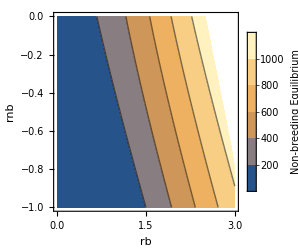

```mathematica
plotX=ListContourPlot[plotDataX,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Non-breeding \nEquilibrium",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```

```mathematica
(* Plot of non-breeding equilibrium *)
plotDataY=raw[[2;;,{2,3,5}]];
```

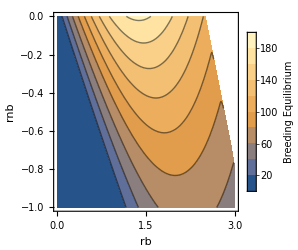

```mathematica
plotY=ListContourPlot[plotDataY,InterpolationOrder->1,
FrameLabel->{"rb","rnb"},
LabelStyle->11,
PlotRange->{{0,3},{-1,0},All},
PlotLegends->Placed[BarLegend[Automatic,
LegendLabel->Style["Breeding \nEquilibrium",11,GrayLevel[0.4]],
LegendMarkerSize->190],
Right],
ImageSize->250
]
```